{2.,2.,1.33333,0.666667,0.266667,0.0888889,0.0253968,0.00634921,0.00141093,0.000282187,0.0000513067,8.55112×10^-6,1.31556×10^-6,1.87937×10^-7,2.50582×10^-8,3.13228×10^-9,3.68503×10^-10,4.09448×10^-11,4.30998×10^-12,4.30998×10^-13,4.10474×10^-14,3.73158×10^-15,3.24486×10^-16,2.70405×10^-17,2.16324×10^-18}

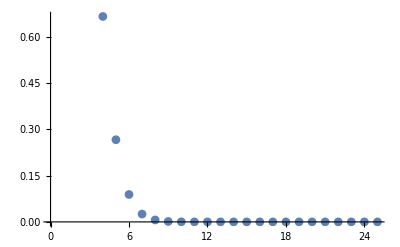

```mathematica
(* Name: *)
(* MATH2262: Analytic Geometry and Calculus II *)
(* Mathematica Project 3 *)

(* 1. Solve problems 137-148 on page 584*)

(* Example *)
(* Subscript[a, n]= n^n/(n!) *)
(* a) Calculate and plot the first 25 terms *)
a[n_]:=N[2^n/n!];
u=Table[a[n],{n,1,25}]
ListPlot[u,PlotMarkers->Automatic]
```

```mathematica
(* b) Find N0 and L such that |Subscript[a, n]-L|≤0.01 *)
L= 0
N0= 15
Table[Abs[a[n]-L],{n,N0,25}]
```

0

15

{2.50582×10^-8,3.13228×10^-9,3.68503×10^-10,4.09448×10^-11,4.30998×10^-12,4.30998×10^-13,4.10474×10^-14,3.73158×10^-15,3.24486×10^-16,2.70405×10^-17,2.16324×10^-18}

x

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000

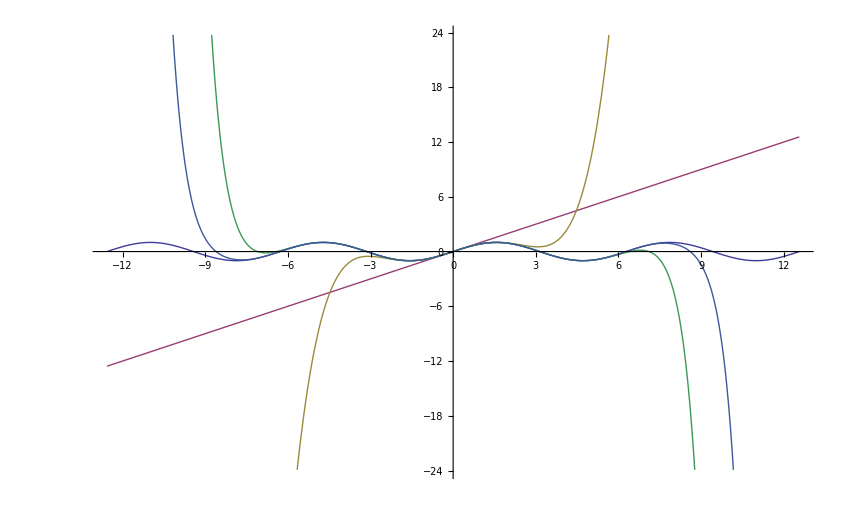

```mathematica
(* 2. For the problems 1 - 32 on page 630 find the Taylor polynomial about x = 0 for N = 1 , 5, 15, 20 and then plot f and the Taylor polynomials on same screen over {{a<=, x≤ b for appropiate values of a and b}}*)

(* Example *)
(* f(x) = Exp[x] *)
Clear[f,P1,P2,P3,x]
f[x_]:=Sin[x];
c=0;
(* DO NOT CHANGE ANYTHING HERE *)
P1[x_]=Normal[Series[f[x],{x,c,1}]]
P5[x_]=Normal[Series[f[x],{x,c,5}]]
P15[x_]=Normal[Series[f[x],{x,c,15}]]
P20[x_]=Normal[Series[f[x],{x,c,20}]]
(* Step 1 *)
Plot[{f[x],P1[x],P5[x],P15[x],P20[x]},{x,-4*Pi,4*Pi},PlotStyle->Thick]
```